```mathematica
s1=plantri[[8]]/.{1->a,2->b,3->c,4->d,5->e}
```

{a<->b,a<->c,a<->d,a<->e,a<->6,b<->6,b<->7,b<->8,b<->c,c<->8,c<->9,c<->10,c<->d,d<->10,d<->11,d<->12,d<->e,e<->12,e<->13,e<->6,6<->13,6<->7,7<->13,7<->14,7<->15,7<->8,8<->15,8<->9,9<->15,9<->16,9<->10,10<->16,10<->11,11<->16,11<->17,11<->12,12<->17,12<->14,12<->13,13<->14,14<->17,14<->15,15<->17,15<->16,16<->17}

```mathematica
s2=s1/.{ 12->1,13->2,7->3,15->4,17->5}
```

{a<->b,a<->c,a<->d,a<->e,a<->6,b<->6,b<->3,b<->8,b<->c,c<->8,c<->9,c<->10,c<->d,d<->10,d<->11,d<->1,d<->e,e<->1,e<->2,e<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5}

```mathematica
s3=s2/.{a->12,b->13,c->7,d->15,e->17}
```

{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5}

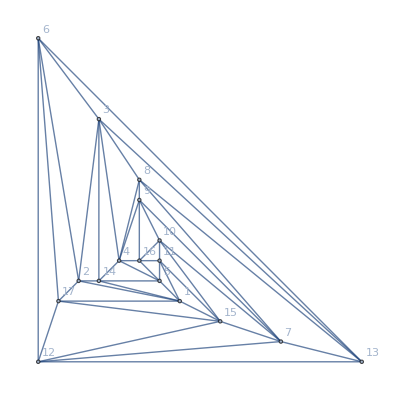

```mathematica
pl8=Graph[s3, VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
MaximalPlanarQ[pl8]
```

True

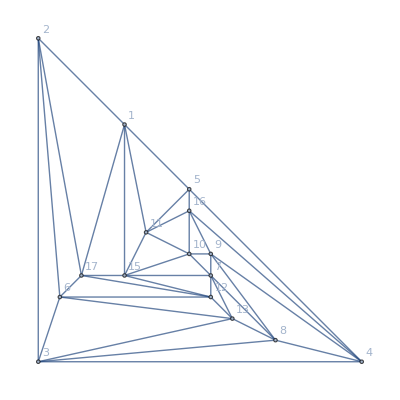

```mathematica
pl8Bis=VertexDelete[pl8,14]
```

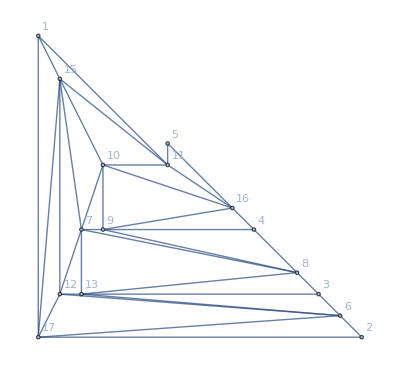

```mathematica
pl8Ter=EdgeDelete[pl8Bis,EdgeList[CycleGraph[5]]]
```

```mathematica
ChromaticPolynomial[pl8,x]==ChromaticPolynomial[Graph[plantri[[8]]],x]
```

True

```mathematica
ChromaticPolynomial[pl8,x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
ChromaticPolynomial[Graph[plantri[[8]]],x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
EmbedGraphInPlantri8Ter[key_]:=Block[{val=allGraphs5[key], sets, reference={12,13,7,15,17}, g, sub,edges},
sets=val["vertexsets"];
g=pl8Ter;
Table[If[Length[s]>1,
g=VertexContract[g,Sort[s]]
], {s,sets}];
sub=val["graph"];
edges=Map[First[sets[[#[[1]]]]]<-> First[sets[[#[[2]]]]]&,EdgeList[sub]];
g=EdgeAdd[g,edges];
Graph[VertexList[g],EdgeList[g],VertexLabels->Table[First[s]->Column[s],{s,sets}],GraphHighlight->edges]
]
```

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
EdgeList[allGraphs5[alfa1Key,"graph"]]
```

{1<->2,1<->3,2<->3}

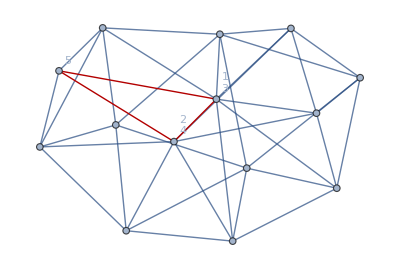

```mathematica
EmbedGraphInPlantri8Ter[alfa1Key]
```

```mathematica
Fulls=Association[]
```

<||>

```mathematica
Table[Fulls[k]=Association[],{k,Keys[allGraphs5]}];
```

```mathematica
Monitor[Table[Fulls[k,"graph"]=EmbedGraphInPlantri8Ter[k],{k,Keys[allGraphs5]}],k];
```

```mathematica
Monitor[Table[Fulls[k,"chromial"]=ChromaticPolynomial[Fulls[k,"graph"],x],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
Monitor[Table[{(Fulls[k,"chromial"]/.x->4)/24,k},{k,Sort[Keys[allGraphs5]]}],k]//Sort
```

{{0,29524},{0,29608},{3,31714},{3,36166},{4,31984},{4,36194},{5,7738},{5,22318},{5,36898},{5,51478},{6,29443},{6,29446},{6,29521},{6,29527},{6,29602},{6,29605},{7,31444},{7,36138},{7,38281},{8,11950},{8,30334},{8,31738},{8,31954},{8,35434},{8,36086},{8,36112},{8,49210},{9,22963},{9,23041},{9,23044},{9,27259},{9,27337},{9,27340},{9,31711},{9,36085},{9,38308},1823,{307,2269},{307,6807},{309,244},{312,2271},{312,6645},{314,2214},{314,6588},{316,732},{316,19764},{328,2430},{328,6562},{342,30},{342,108},{354,2188},{354,6804},{355,82},{355,246},{364,4},{364,324},{364,8748},{368,9},{368,2190},{368,6642},{385,84},{388,729},{388,19683},{392,2268},{392,6564},{423,27},{436,1},{436,243},{464,2187},{464,6561},{488,3},{488,81},{628,0}}
 |  |  |  |

```mathematica
ShowGraph[allGraphs5,31714]
```

-Graphics-31714

```mathematica
ShowGraph[allGraphs5,29608]
```

-Graphics-29608

```mathematica
ShowGraph[allGraphs5,36166]
```

-Graphics-36166

```mathematica
ShowGraph[allGraphs5,31984]
```

-Graphics-31984

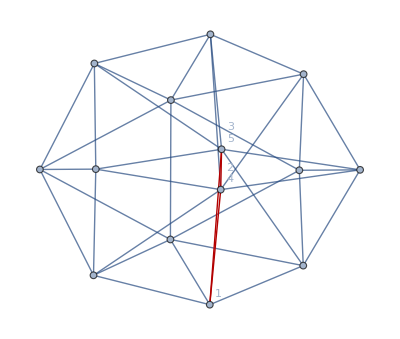

```mathematica
alfa1Embedded=EmbedGraphInPlantri8Ter[29608]
```

```mathematica
ChromaticPolynomial[alfa1Embedded,4]
```

0

```mathematica
Table[ChromaticPolynomial[EdgeDelete[alfa1Embedded,e],4]->e,{e,EdgeList[alfa1Embedded]}]//Sort
```

{48→8<->9,48→9<->16,48→11<->1,48→11<->16,48→13<->6,48→13<->8,48→17<->1,48→17<->6,72→7<->15,96→2<->6,96→2<->16,96→3<->6,96→3<->16,120→1<->2,120→1<->3,120→2<->8,120→3<->8,144→7<->9,144→7<->10,144→9<->10,144→10<->11,144→10<->16,144→12<->6,144→12<->7,144→12<->13,144→12<->15,144→12<->17,144→13<->7,144→15<->10,144→15<->11,144→15<->17,168→7<->8,168→15<->1,192→2<->9,192→2<->17,192→3<->11,192→3<->13,264→2<->3}

```mathematica
Table[ChromaticPolynomial[EdgeContract[alfa1Embedded,e],4]->e,{e,EdgeList[alfa1Embedded]}]//Sort
```

{48→8<->9,48→9<->16,48→11<->1,48→11<->16,48→13<->6,48→13<->8,48→17<->1,48→17<->6,72→7<->15,96→2<->6,96→2<->16,96→3<->6,96→3<->16,120→1<->2,120→1<->3,120→2<->8,120→3<->8,144→7<->9,144→7<->10,144→9<->10,144→10<->11,144→10<->16,144→12<->6,144→12<->7,144→12<->13,144→12<->15,144→12<->17,144→13<->7,144→15<->10,144→15<->11,144→15<->17,168→7<->8,168→15<->1,192→2<->9,192→2<->17,192→3<->11,192→3<->13,264→2<->3}